```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes"]
```

C:\Users\pglpm\repositories\genobayes

```mathematica
NS["study_dirichlet_type_iii_2"]
```

```mathematica
nn=5*10^6;
```

```mathematica
data=Import["scripts\\dataset1_simple.csv"];
n=Length[data[[;;,1]]];
Dimensions[data]
```

{6029,97}

```mathematica
ClearAll[fs];fs[ng_]:=fs[ng]=
SortBy[Tally[data[[;;,Join[{1,2,3},ng]]]],FromDigits[#[[1]],2]&][[;;,2]]/n
```

```mathematica
fs[Range[4]]
```

{1839/6029,588/6029,303/6029,93/6029,841/6029,261/6029,340/6029,103/6029,454/6029,173/6029,50/6029,23/6029,317/6029,111/6029,393/6029,140/6029}

```mathematica
ddir[aa_,nx_,f_]:=Block[{t=Length[f],n2=nx+aa,f2},
(Multinomial@@(nx*f))*Gamma[aa]/Gamma[n2]*(Times@@Gamma[nx*f+aa/t])/Gamma[aa/t]^t]
```

```mathematica
ClearAll[con];con[f_]:=con[f]=1/NIntegrate[ddir[ax,n,f],{ax,0,10^6}]
```

```mathematica
ClearAll[nddir];nddir[aa_,nx_,f_]:=ddir[aa,nx,f]*con[f]
```

```mathematica
list0=FoldList[Join,{6},T@{{57,32,66,75,88,93,22,14,21,43,89,70,90}}]
```

{{6},{6,57},{6,57,32},{6,57,32,66},{6,57,32,66,75},{6,57,32,66,75,88},{6,57,32,66,75,88,93},{6,57,32,66,75,88,93,22},{6,57,32,66,75,88,93,22,14},{6,57,32,66,75,88,93,22,14,21},{6,57,32,66,75,88,93,22,14,21,43},{6,57,32,66,75,88,93,22,14,21,43,89},{6,57,32,66,75,88,93,22,14,21,43,89,70},{6,57,32,66,75,88,93,22,14,21,43,89,70,90}}

```mathematica
listsample:=Block[{rsam=RandomSample[Range[94],Length@Last[list0]]},FoldList[Join,{rsam[[1]]},T@{rsam[[2;;]]}]]
```

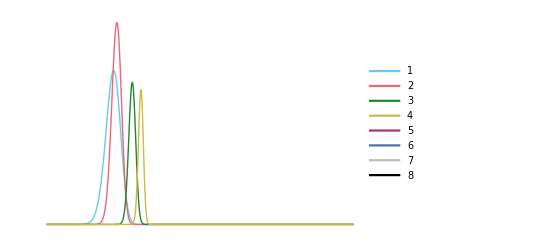

```mathematica
fixLogPlots@LogLinearPlot[Evaluate@Table[nddir[ax,n,fs[k]],{k,list}],{ax,1,10^6},PlotRange->All,Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | "insomnia data"],None},{A,None}}]
```

```mathematica
listsample0=listsample;
```

```mathematica
gtab=Table[fixLogPlots@LogLogPlot[ddir[ax,n,fs[k]],{ax,1,10^6},PlotRange->Auto,Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],
PlotLegends->Auto,FrameLabel->{{p[A | Length[k]],None},{A,None}}],{k,listsample0}];
```

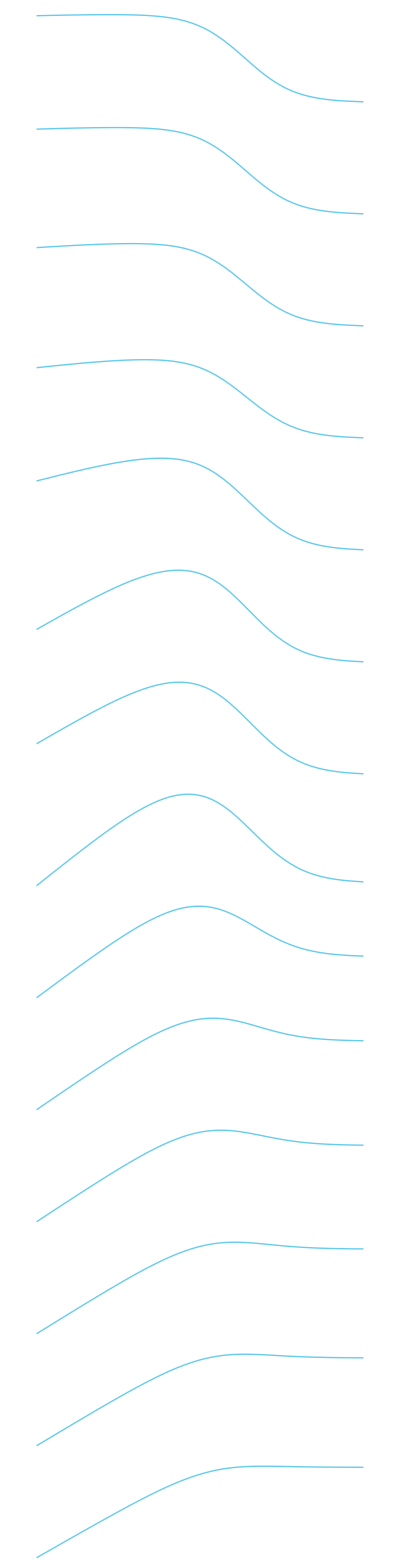
(-Graphics-)

```mathematica
gtab//MF
```

```mathematica
tabm0=Table[{Length[i]+3,2^Length[i]*8/2},{i,list0}]
```

{{4,8},{5,16},{6,32},{7,64},{8,128},{9,256},{10,512},{11,1024},{12,2048},{13,4096},{14,8192},{15,16384},{16,32768},{17,65536}}

```mathematica
ClearAll[tabmax];tabmax[0]=Table[{Length[i]+3,ax/.NMaximize[{Log@ddir[ax,n,fs[i]],1<ax<10^5},ax][[2]]},{i,list0}];
```

```mathematica
tabmax[k_]:=tabmax[k]=Table[{Length[i]+3,ax/.NMaximize[{Log@ddir[ax,n,fs[i]],1<ax<10^5},ax][[2]]},{i,listsample}];
```

```mathematica
tabmax[1]
```

{{4,21.7867},{5,35.3154},{6,66.6594},{7,86.4133},{8,178.991},{9,374.074},{10,703.442},{11,1491.8},{12,1574.25},{13,2289.82},{14,3562.82},{15,8985.31},{16,10142.1}}

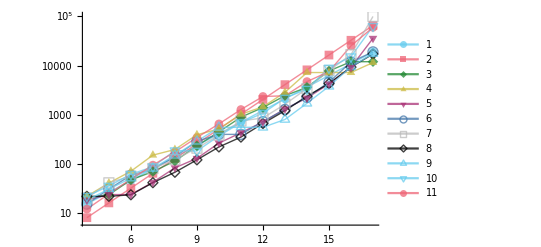

```mathematica
ListLogPlot[Join[{tabfit,tabm0},Table[tabmax[r],{r,0,8}]],PlotRange->All,PlotStyle->Opacity[0.75],PlotLegends->Auto,PlotMarkers->Auto,Joined->True]
```

```mathematica
expdf["testfit",%]
```

testfit.pdf

```mathematica
Table[tabmax[r],{r,0,10}]//MF
```

((4
20.3802) | (5
23.4772) | (6
47.0858) | (7
69.393) | (8
113.959) | (9
232.142) | (10
448.031) | (11
891.178) | (12
1401.23) | (13
2437.03) | (14
3611.61) | (15
7770.47) | (16
11998.2) | (17
11998.2)
(4
21.8799) | (5
40.6409) | (6
70.6076) | (7
150.333) | (8
195.629) | (9
390.678) | (10
511.725) | (11
1021.63) | (12
1447.11) | (13
2858.22) | (14
7218.44) | (15
7218.44) | (16
7218.44) | (17
11531.)
(4
18.2537) | (5
23.6521) | (6
23.6521) | (7
42.1483) | (8
82.7681) | (9
129.332) | (10
263.901) | (11
429.822) | (12
712.56) | (13
1310.3) | (14
2188.17) | (15
4233.48) | (16
9203.62) | (17
35903.)
(4
15.1291) | (5
30.5808) | (6
58.6269) | (7
77.9051) | (8
140.021) | (9
287.477) | (10
397.633) | (11
397.633) | (12
725.212) | (13
1279.38) | (14
2256.26) | (15
4577.9) | (16
11836.2) | (17
18997.4)
(4
20.1116) | (5
41.0428) | (6
56.0617) | (7
80.3123) | (8
122.687) | (9
208.245) | (10
383.806) | (11
747.528) | (12
857.208) | (13
1632.87) | (14
3390.78) | (15
7903.25) | (16
16706.3) | (17
100000.)
(4
21.7857) | (5
21.7857) | (6
23.4326) | (7
41.2947) | (8
67.3499) | (9
120.463) | (10
220.512) | (11
350.061) | (12
662.336) | (13
1205.54) | (14
2377.8) | (15
4304.29) | (16
9294.44) | (17
17178.5)
(4
18.2537) | (5
30.5032) | (6
51.2459) | (7
80.7681) | (8
149.103) | (9
287.644) | (10
551.281) | (11
553.634) | (12
553.634) | (13
799.136) | (14
1707.52) | (15
3782.6) | (16
9423.38) | (17
17597.8)
(4
21.9089) | (5
35.3867) | (6
61.2895) | (7
87.1097) | (8
185.637) | (9
182.251) | (10
369.758) | (11
690.233) | (12
1074.91) | (13
2180.05) | (14
3317.64) | (15
8934.9) | (16
15197.7) | (17
63199.1)
(4
11.9786) | (5
24.4075) | (6
48.7793) | (7
93.9224) | (8
175.113) | (9
343.237) | (10
649.21) | (11
1273.66) | (12
2349.77) | (13
2424.68) | (14
4722.23) | (15
7540.27) | (16
25208.5) | (17
59937.8)
(4
17.6059) | (5
22.6547) | (6
43.0852) | (7
82.5168) | (8
129.412) | (9
269.083) | (10
376.631) | (11
564.137) | (12
781.139) | (13
1354.53) | (14
2241.14) | (15
3224.5) | (16
5013.21) | (17
5013.21)
(4
10.4406) | (5
11.2936) | (6
20.7761) | (7
38.8623) | (8
72.3027) | (9
134.82) | (10
251.176) | (11
506.524) | (12
804.048) | (13
1638.33) | (14
3671.17) | (15
4227.82) | (16
9705.15) | (17
15549.3))

```mathematica
Fit[Flatten[Table[Table[{tabmax[r][[i,1]],Log[2,tabmax[r][[i,2]]]},{i,Length@tabmax[0]}],{r,0,8}],1],{1,x},x]
```

0.770361+0.789061 x

```mathematica
tabfit=Table[{Length[i]+3,2^(0.77+0.79*(Length[i]+3))},{i,list0}]
```

{{4,15.2422},{5,26.3549},{6,45.5696},{7,78.7932},{8,136.239},{9,235.568},{10,407.315},{11,704.277},{12,1217.75},{13,2105.58},{14,3640.7},{15,6295.04},{16,10884.6},{17,18820.3}}

```mathematica
tabmax2=tabmax;
```

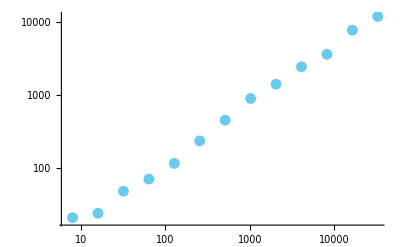

```mathematica
ListLogLogPlot[T@{tabmax[[;;,1]]*8/2,tabmax[[;;,2,2,1,2]]},PlotRange->All]
```

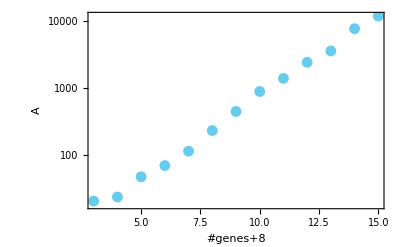

```mathematica
ListLogPlot[T@{Log[2,tabmax[[;;,1]]*8/2],tabmax[[;;,2,2,1,2]]},PlotRange->All,Frame->True,Axes->None,FrameLabel->{{A,None},{"#genes+8",None}}]
```

```mathematica
expdf["A_vs_n-genes"]
```

A_vs_n-genes.pdf

```mathematica
Fit[T@{Log[2,tabmax[[;;,1]]*8],Log[10,tabmax[[;;,2,2,1,2]]]},{1,x},x]
```

0.205851+0.243238 x

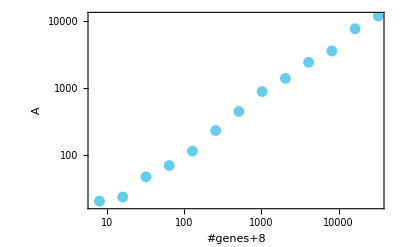

```mathematica
ListLogLogPlot[T@{tabmax[[;;,1]]*8/2,tabmax[[;;,2,2,1,2]]},PlotRange->All,Frame->True,Axes->None,FrameLabel->{{A,None},{"#genes+8",None}}]
```

```mathematica
ddir[10,n,fs[3]]//N
```

1.9953038373×10^-23

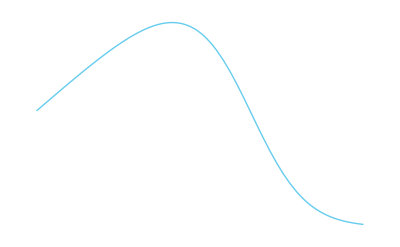

```mathematica
fixLogPlots@LogLogPlot[ddir[ax,n,fs[3+15]],{ax,1,10^6},PlotRange->All,Frame->Auto,Axes->None,FrameStyle->Directive[Black,Bold,18],FrameLabel->{{p[A | "insomnia data"],None},{A,None}}]
```

```mathematica
expdf["A_from_insomniadata",%]
```

A_from_insomniadata.pdf

```mathematica
NIntegrate[
```

```mathematica
avfs=NIntegrate[(n*fs+ax/8)/(n+ax)*ddir[ax,n,fs],{ax,0,10^6}]
```

{1.03321×10^-22,2.67437×10^-23,4.69515×10^-23,1.69163×10^-23,1.82777×10^-23,1.89158×10^-23,3.17498×10^-24,2.27446×10^-23}

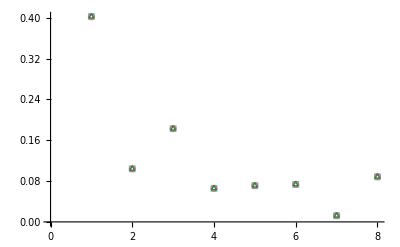

```mathematica
ListPlot[{fs,avfs*con[fs],(n*fs+1/2)/(n+8/2)},PlotRange->{0,All},PlotMarkers->{□,○,△}]
```

```mathematica
NIntegrate[ddir[ax,n,Table[1,8]/8 ]*con[Table[1,8]/8 ],{ax,0,10^6}]
```

1.

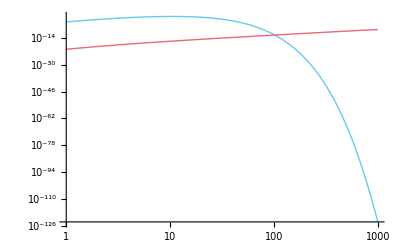

```mathematica
LogLogPlot[{ddir[ax,n,fs]*con[fs],ddir[ax,n,Table[1,8]/8 ]*con[Table[1,8]/8]},{ax,1,10^3},PlotRange->All]
```

```mathematica
ddir2[aa_,nx_,t_]:=(nx!)*Gamma[aa]/Gamma[nx+aa]*Gamma[aa/t+1]^nx*Gamma[aa/t]^(-nx)
```

```mathematica
lddir2[aa_,nx_,t_]:=Log[nx!]+Log@Gamma[aa]-Log@Gamma[nx+aa]+nx*Log@Gamma[aa/t+1]-nx*Log@Gamma[aa/t]
```

```mathematica
lddir2[10^29,n,2^10]//N
```

Overflow[]

```mathematica
Limit[lddir2[ax,n,2^94],ax->+Infinity]//N
```

-346370.

```mathematica
Assuming[nx>0&&t>0,FS@Series[lddir2[ax,nx,t],{ax,+Infinity,0}]]
```

Log[nx!]+Log[ⅇ^((-1+Log[ax]) ax+O[1/ax]^2) (√(2 π) √(1/ax)+O[1/ax]^(3/2))]-Log[ax^nx ⅇ^((-1+Log[ax]) ax+O[1/ax]^2) (√(2 π) √(1/ax)+O[1/ax]^(3/2))]-nx Log[ⅇ^(((-1+Log[ax]-Log[t]) ax)/t+O[1/ax]^2) (√(2 π) √t √(1/ax)+O[1/ax]^(3/2))]+nx Log[ⅇ^(((-1+Log[ax]-Log[t]) ax)/t+O[1/ax]^2) ((√(2 π) √ax)/(√t)+1/6 √(π/2) √t √(1/ax)+O[1/ax]^(3/2))]

```mathematica
Assuming[nx>0&&t>0,FS@Series[ddir2[ax,nx,t],{ax,+Infinity,1}]]
```

ax^-nx Gamma[ax/t]^-nx Gamma[(ax+t)/t]^nx (nx!-((-1+nx) nx nx!)/(2 ax)+O[1/ax]^2)

```mathematica
limddir2[ax_,nx_,t_]=Assuming[nx>0&&t>0&&ax>0,FS@Normal[%]]
```

((2 ax+nx-nx^2) t^-nx nx!)/(2 ax)

```mathematica
Maximize[limddir2[ax,nx,t],ax,Reals]
```

Maximize[((2 ax+nx-nx^2) t^-nx nx!)/(2 ax),ax,ℝ]

```mathematica
Assuming[nx>0&&t>0&&ax>0,FS@D[ddir2[ax,nx,t],ax]]
```

1/(ax Gamma[ax+nx])(ax/t)^nx Gamma[ax] Gamma[1+nx] (nx+ax PolyGamma[0,ax]-ax PolyGamma[0,ax+nx])

```mathematica
Reduce[%==0,ax]
```

Reduce[1/(ax Gamma[ax+nx])(ax/t)^nx Gamma[ax] Gamma[1+nx] (nx+ax PolyGamma[0,ax]-ax PolyGamma[0,ax+nx])==0,ax]

```mathematica
FindMaximum[limddir2[ax,n,2^30],ax]
```

{-9.78760360266851×10^-34266,{ax→1.}}

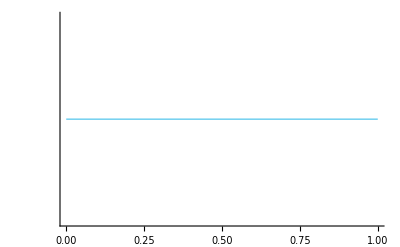

```mathematica
LogPlot[limddir2[1/ax,n,2^94],{ax,0,10^-20},PlotRange->All]
```

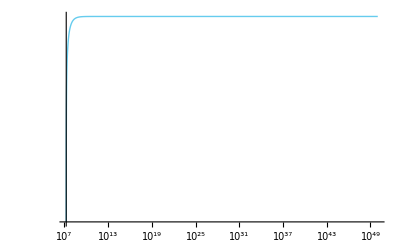

```mathematica
LogLogPlot[limddir2[ax,n,2^94],{ax,10^3,10^50},PlotRange->All]
```

```mathematica
Log@ddir2[10^6,n,2^94]//N
```

-346388.

```mathematica
Log[10,2^50]//N
```

15.0515

```mathematica
FindMaximum[lddir2[ax,n,2^30],ax]
```

{-78915.3,{ax→3.83508×10^7}}

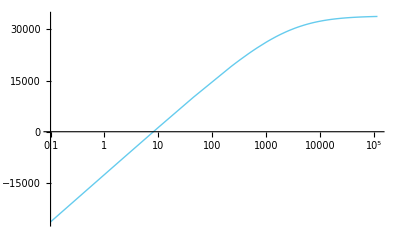

```mathematica
LogLinearPlot[Log@ddir2[ax,n,2^3],{ax,0.1,10^32},PlotRange->All]
```

```mathematica
(* expected freq *)
ms[aa_,nx_]=(nx*fs+aa/ts)/(nx+aa);
```

```mathematica
qs[aa_,nx_]=FS@Table[{{i,ms[aa,nx][[i]]},ErrorBar[Quantile[BetaDistribution[(aa+nx)*ms[aa,nx][[i]],(aa+nx)*(1-ms[aa,nx][[i]])],{5/100,95/100}]-ms[aa,nx][[i]]]},{i,rs}];
```

```mathematica
qs[10,10]//N
```

{{{1.,0.263777},ErrorBar[{-0.14379,0.171234}]},{{2.,0.114499},ErrorBar[{-0.0887997,0.132794}]},{{3.,0.153892},ErrorBar[{-0.107193,0.147037}]},{{4.,0.0953413},ErrorBar[{-0.0783011,0.12414}]},{{5.,0.0979951},ErrorBar[{-0.0798291,0.125424}]},{{6.,0.0992391},ErrorBar[{-0.0805367,0.126015}]},{{7.,0.0685541},ErrorBar[{-0.0612622,0.109202}]},{{8.,0.106703},ErrorBar[{-0.0846715,0.129437}]}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
aarange=10^Join[{-2},Range[0,6,2]];nxrange=10^Join[{-Infinity},Range[0,6,2]];tab=Table[ErrorListPlot[qs[aai,nxi],PlotRange->{{0.5,8.5},{0,1}},ErrorBarFunction->Function[{coords, errs}, {Opacity[0.5],red,Rectangle[coords+{-0.05,errs⟦2,1⟧},coords+{0.05,errs⟦2,2⟧}]}],Frame->Auto,FrameTicks->{Range[1,8],Auto},FrameLabel->{If[aai==Last[aarange],Style["n",Italic]==nxi,None],If[nxi==First[nxrange],A == aai,None]},ImageSize->a5rsize],{aai,aarange},{nxi,nxrange}];
```

```mathematica
grid=Labeled[GraphicsGrid[tab],{Style[symptom,24],Rotate[Style["mean freq. & 90% quantile",24],Pi/2]},{Bottom,Left}];
```

```mathematica
expdf0["test",Show[grid]]
```

test.pdf

```mathematica
(* study of gene data *)
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Series[InverseBetaRegularized[1/20,k,aa+nx],{k,0,2}]
```

InverseBetaRegularized[1/20,k,aa+nx]

```mathematica
Plot[InverseBetaRegularized[1/20,k,10],{k,0,1}]
```

$Aborted

```mathematica
tg=2^94;rg={0,1};
mg[aa_,nx_]=FS[({0,Boole[nx≥1]}+aa/tg)/(nx+aa)];
```

```mathematica
qb[aa_,nx_,0]=(mmm=mg[aa,nx][[1]];{mmm,mmm});qb[aa_,nx_,1]=(mmm=mg[aa,nx][[2]];Quantile[BetaDistribution[(aa+nx)*mmm,(aa+nx)*(1-mmm)],{5/100,95/100}])
```

{InverseBetaRegularized[1/20,aa/19807040628566084398385987584+Boole[nx≥1],(aa+nx) (1-(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx))],InverseBetaRegularized[19/20,aa/19807040628566084398385987584+Boole[nx≥1],(aa+nx) (1-(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx))]}

```mathematica
qb[10,10,0]//N
```

{2.52435×10^-29,2.52435×10^-29}

```mathematica
qg[aa_,nx_]=FS@Table[mmm=mg[aa,nx][[i]];{{i-1,mmm},ErrorBar[qb[aa,nx,i-1]-mmm]},{i,rg+1}]
```

{{{0,aa/(19807040628566084398385987584 (aa+nx))},ErrorBar[{0,0}]},{{1,(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx)},ErrorBar[{-(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx)+InverseBetaRegularized[1/20,aa/19807040628566084398385987584+Boole[nx≥1],(aa+nx) (1-(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx))],-(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx)+InverseBetaRegularized[19/20,aa/19807040628566084398385987584+Boole[nx≥1],(aa+nx) (1-(aa/19807040628566084398385987584+Boole[nx≥1])/(aa+nx))]}]}}

```mathematica
mg[10,10]//N
```

{2.52435×10^-29,0.05}

```mathematica
qg[0.1,0]//N
```

$Aborted

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
aarange=10^Join[{-2},Range[0,6,2]];nxrange=10^Join[{},Range[0,6,2]];tabg=Table[ErrorListPlot[qg[aai,nxi],PlotRange->{{-0.5,1.5},{0,1}},Axes->None,ErrorBarFunction->Function[{coords, errs}, {Opacity[0.5],red,Rectangle[coords+{-0.05,errs⟦2,1⟧},coords+{0.05,errs⟦2,2⟧}]}],Frame->Auto,FrameTicks->{{Auto,None},{Range[0,1],None}},FrameLabel->{If[aai==Last[aarange],Style["n",Italic]==nxi,None],If[nxi==First[nxrange],A == aai,None]},ImageSize->a5rsize],{aai,aarange},{nxi,nxrange}];
```

```mathematica
gridg=Labeled[GraphicsGrid[tabg],{Style[symptom,24],Rotate[Style["mean freq. & 90% quantile",24],Pi/2]},{Bottom,Left}];
```

```mathematica
expdf0["testg",Show[gridg]]
```

testg.pdf

```mathematica
Log[2,30]//N
```

4.90689

```mathematica
2^5//N
```

32.

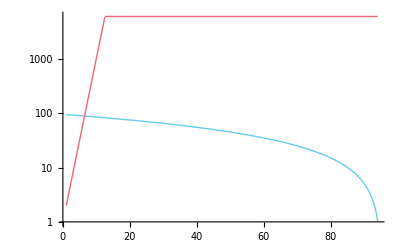

```mathematica
LogPlot[{95-i,Min[2^i,n]},{i,1,94},PlotRange->All]
```

```mathematica
Solve[95-i==Min[2^i,n],i]//N
```

{{i→6.46813}}

```mathematica
2^7
```

128

```mathematica
st[aa_,nx_]=FS@Sqrt[(nf[aa,nx]*(1-nf[aa,nx]))/(nx+aa+1)];
```

```mathematica
Plot3D[Evaluate@nf[10^laa,10^lnx],{laa,-2,6},{lnx,-6,6},PlotRange->All,AxesLabel->{ld[A],ld["n"]},BoxRatios->{3,3,2},Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate@nf[aa,nx],{aa,0.0001,10^3},{nx,0,10^3},PlotRange->All,AxesLabel->{A,"n"},BoxRatios->{3,3,2},Mesh->None]
```

-Graphics3D-

```mathematica
es[aa_,nx_]=Assuming[aa>0&&nx>0,FS[Log[(Times@@Gamma[(aa+nx)*nf[aa,nx]])/Gamma[aa+nx]]
-Total[((aa+nx)*nf[aa,nx]-1)*(PolyGamma[(aa+nx)*nf[aa,nx]]-PolyGamma[aa+nx])]]];
```

```mathematica
Plot3D[es[10^aa,10^nx],{aa,-2,6},{nx,-2,6},PlotRange->All,AxesLabel->{A,"n"},BoxRatios->{3,3,2},Mesh->None]
```

$Aborted

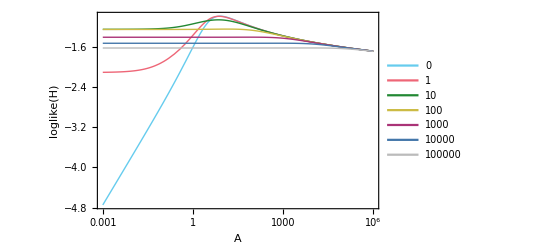

```mathematica
fixLogPlots@LogLinearPlot[Evaluate@Table[slog@es[aa,10^nx],{nx,Join[{-Infinity},Range[0,5]]}],{aa,10^-3,10^6},PlotRange->All,PlotLegends->Placed[10^Join[{-Infinity},Range[0,5]],{{0.9,0.1},{0.9,0.1}}],Frame->True,FrameLabel->{A,loglike[H]}]
```

```mathematica
expdf["entropy_symptoms_An"]
```

entropy_symptoms_An.pdf

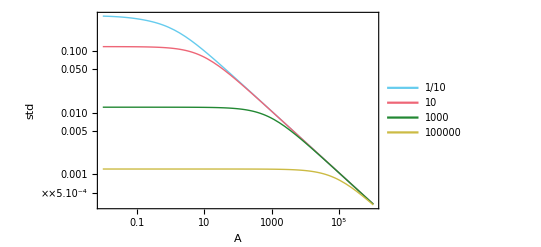

```mathematica
fixLogPlots@LogLogPlot[Evaluate@Table[st[aa,10^nx][[3]],{nx,Range[-1,5,2]}],{aa,10^-2,10^6},PlotRange->All,PlotLegends->Placed[10^Range[-1,5,2],{{0.9,0.9},{0.9,0.9}}],Frame->True,FrameLabel->{A,std}]
```

```mathematica
expdf["std3_symptoms_An"]
```

std3_symptoms_An.pdf

```mathematica
f=Table[Count[ds,i],{i,rgs}]/n
```

{2427/6029,627/6029,1102/6029,396/6029,428/6029,443/6029,73/6029,533/6029}

```mathematica
tg=2^94;
```

```mathematica
nfg[aa_,nx_]=FS[({0,Boole[nx≥1]}+aa/tg)/(nx+aa)];
```

```mathematica
stg[aa_,nx_]=FS@Sqrt[(nfg[aa,nx]*(1-nfg[aa,nx]))/(nx+aa+1)];
```

```mathematica
nfg[10^-2,10^-6]//N
```

{5.0482×10^-29,5.0482×10^-29}

```mathematica
Plot3D[Evaluate@nfg[10^laa,10^lnx],{laa,-2,6},{lnx,-1,6},PlotRange->All,AxesLabel->{ld[A],ld["n"]},BoxRatios->{3,3,2},Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[Evaluate@nf[aa,nx],{aa,0.0001,10^3},{nx,0,10^3},PlotRange->All,AxesLabel->{A,"n"},BoxRatios->{3,3,2},Mesh->None]
```

-Graphics3D-

```mathematica
eg[aa_,nx_]=Assuming[aa>0&&nx>0,FS[(({tg-nx,nx}.Log[Gamma[(aa+nx)*nfg[aa,nx]]])-Log[Gamma[aa+nx]])
-Total[{tg-nx,nx}*((aa+nx)*nfg[aa,nx]-1)*(PolyGamma[(aa+nx)*nfg[aa,nx]]-PolyGamma[aa+nx])]]];
```

```mathematica
Plot3D[es[10^aa,10^nx],{aa,-2,6},{nx,-2,6},PlotRange->All,AxesLabel->{A,"n"},BoxRatios->{3,3,2},Mesh->None]
```

$Aborted

```mathematica
slog[x_]=Sign[x]*Log[10,Abs@x+1]
```

(Log[1+Abs[x]] Sign[x])/Log[10]

```mathematica
eg[10^3,tg]//N
```

Overflow[]

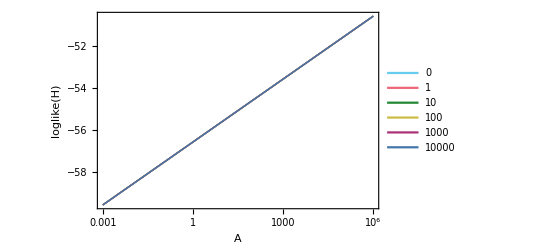

```mathematica
fixLogPlots@LogLinearPlot[Evaluate@Table[slog@eg[aa,10^nx],{nx,Join[{-Infinity},Range[0,4]]}],{aa,10^-3,10^6},PlotRange->All,PlotLegends->Placed[10^Join[{-Infinity},Range[0,4]],{{0.2,0.01},{0.2,0.01}}],Frame->True,FrameLabel->{A,loglike[H]}]
```

```mathematica
expdf["entropy_genes_An"]
```

entropy_genes_An.pdf

```mathematica
qt[aa_]=Quantile[BetaDistribution[aa/2,aa/2],{1/8,7/8}]
```

{InverseBetaRegularized[1/8,aa/2,aa/2],InverseBetaRegularized[7/8,aa/2,aa/2]}

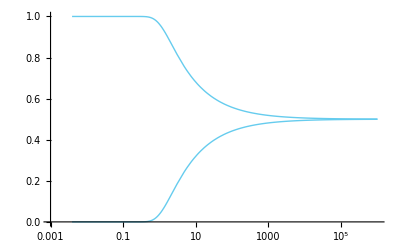

```mathematica
LogLinearPlot[qt[aa],{aa,10^-3,10^6}]
```

```mathematica
fixLogPlots@LogLogPlot[Evaluate@Table[st[aa,10^nx][[3]],{nx,Range[-1,5,2]}],{aa,10^-2,10^6},PlotRange->All,PlotLegends->Placed[10^Range[-1,5,2],{{0.9,0.9},{0.9,0.9}}],Frame->True,FrameLabel->{A,std}]
```

-Graphics-

```mathematica
expdf["std3_symptoms_An"]
```

std3_symptoms_An.pdf

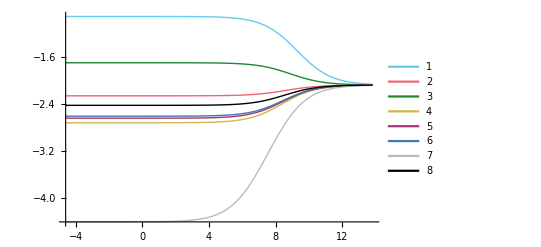

```mathematica
fixLogPlots@LogLogPlot[Evaluate@nf[aa],{aa,0.01,10^6},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Auto,Frame->Auto,FrameLabel->{A,"expected frequency"}]
```

```mathematica
expdf["log_mean_freq_A"]
```

log_mean_freq_A.pdf

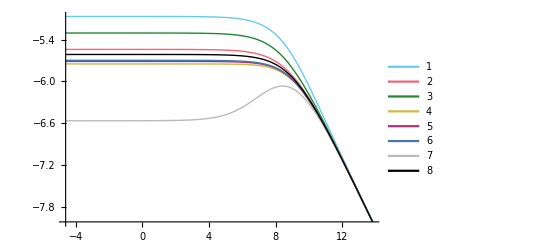

```mathematica
fixLogPlots@LogLogPlot[Evaluate@st[aa],{aa,0.01,10^6},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Auto,Frame->Auto,FrameLabel->{A,"std"}]
```

```mathematica
expdf["log_std_freq_A"]
```

log_std_freq_A.pdf

```mathematica
nfg[aa_]=(n*1/n+aa/2^94)/(n+aa);
```

```mathematica
stg[aa_]=FS@Sqrt[(nfg[aa]*(1-nfg[aa]))/(n+aa+1)];
```

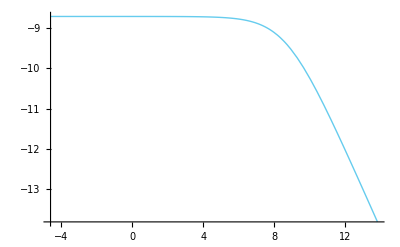

```mathematica
fixLogPlots@LogLogPlot[Evaluate@nfg[aa],{aa,0.01,10^6},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Auto,Frame->Auto,FrameLabel->{A,"expected frequency"}]
```

```mathematica
expdf["mean_freq_gA"]
```

mean_freq_gA.pdf

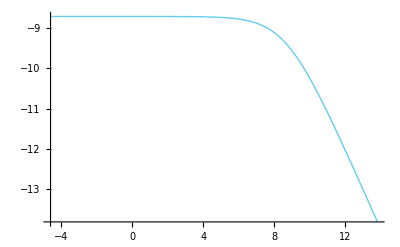

```mathematica
fixLogPlots@LogLogPlot[Evaluate@stg[aa],{aa,0.01,10^6},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Auto,Frame->Auto,FrameLabel->{A,"std"}]
```

```mathematica
expdf["std_freq_gA"]
```

std_freq_gA.pdf

```mathematica
nfn[aa_]=n/nn*f+(nn-n)/nn*(n*f+aa/8)/(n+aa);
```

```mathematica
stn[aa_]=FS@Sqrt[
(nn+n+aa)/(nn*(n+aa+1))*(n*f+aa/8)/(n+aa)*(1-(n*f+aa/8)/(n+aa))];
```

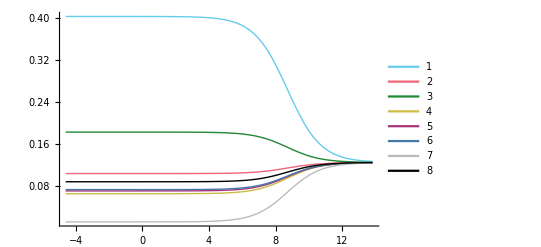

```mathematica
fixLogPlots@LogLinearPlot[Evaluate@nfn[aa],{aa,0.01,10^6},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Auto,Frame->Auto,FrameLabel->{A,"expected frequency"}]
```

```mathematica
expdf["mean_freq_NA"]
```

mean_freq_NA.pdf

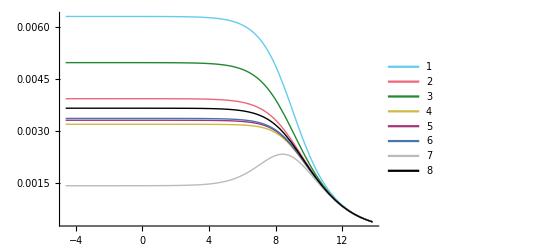

```mathematica
fixLogPlots@LogLinearPlot[Evaluate@stn[aa],{aa,0.01,10^6},AxesOrigin->{0,0},PlotRange->All,PlotLegends->Auto,Frame->Auto,FrameLabel->{A,"std"}]
```

```mathematica
expdf["std_freq_NA"]
```

std_freq_NA.pdf

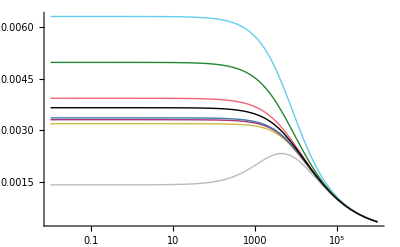

```mathematica
fixLogPlots@LogLinearPlot[Evaluate@st[aa],{aa,0.01,10^6},PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
data[[1]]
```

{ï»¿IID,SEX,AGE,GROUP,rs697680_A,rs228729_T,rs11121023_A,rs10864315_T,rs170631_G,rs875994_C,rs228682_C,rs228666_C,rs228669_T,rs228688_T,rs228690_T,rs10462018_T,rs228692_A,rs697690_C,rs2640908_T,rs4663866_C,rs934945_T,rs2304669_C,rs10462023_A,rs11894491_A,rs13002160_T,rs10462028_A,rs1801260_G,rs3792603_G,rs11133383_C,rs11932595_G,rs13113518_C,rs900144_C,rs4414197_T,rs7950226_A,rs10832020_C,rs11022761_T,rs11022762_T,rs7126796_C,rs10766077_A,rs7924734_G,rs10832027_G,rs1026071_G,rs12421530_C,rs2290036_C,rs1868049_T,rs3789327_G,rs11022778_G,rs3816358_A,rs4757151_A,rs12363415_G,rs11022781_A,rs969485_G,rs11022783_A,rs17452383_G,rs7121611_T,rs7121775_C,rs2292913_A,rs11038698_C,rs11038699_G,rs2292910_A,rs3824872_A,rs17441402_T,rs703829_T,rs11171846_T,rs11171856_C,rs714359_A,rs12821586_A,rs11113153_T,rs3741892_C,rs10861688_T,rs12368868_G,rs2585408_T,rs2735611_G,rs3027178_G,rs3027171_A,rs2518023_T,rs3027160_C,rs4794826_T,rs883871_A,rs2102928_T,rs2071427_T,rs2269457_C,rs4795424_C,rrs2797687_T,rrs2794664_A,rrs228730_A,rrs228697_G,rrs6858749_T,rrs2412646_T,rrs11240_G,rrs2070062_C,rrs6486120_T,rrs5443_T,rrs7958822_A,rrs922270_C,rrs4964057_G,rrs11071547_T,rrs3848543_T}

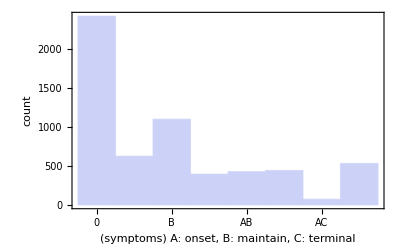

```mathematica
Histogram[data[[2;;,4]],PlotRange->All,FrameTicks->{{Auto,None},{{{1,"0"},{2,"A"},{3,"B"},{4,"C"},{5,"AB"},{6,"BC"},{7,"AC"},{8,"ABC"}},None}},Frame->{True,True},FrameLabel->{"(symptoms) A: onset, B: maintain, C: terminal","count"}]
```

```mathematica
expdf["histogram_insomnia"]
```

histogram_insomnia.pdf

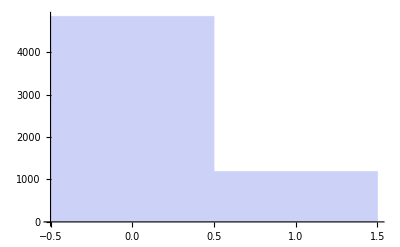

```mathematica
Histogram[data[[2;;,9]],PlotRange->All]
```

```mathematica
subd[gen_,val_]:=Pick[data,(#==val)&/@data[[;;,gen]],True]
```

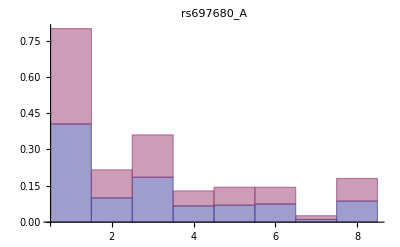
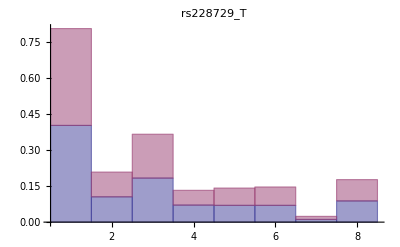

```mathematica
Table[Histogram[subd[var,#][[;;,sym]]&/@{0,1},Auto,"Probability",ChartLayout->"Stacked",PlotLabel->mystyle[data[[1,var]]]],{var,5,6}]
```

```mathematica
applyhist[data_,label_]:=Block[{dat=Pick[data,Map[(Length[#]>0)&,data],True]},(BarChart[Last/@#//Transpose,PlotLabel->label,ChartLabels->{Range[1,8],Auto},ChartLegends->Placed[Length/@dat,Below],PlotRange->All(*,FrameLabel->{"symptom",None},Frame->{True,True,False,False}*)]
&@(HistogramList[#,{1,8,1},"Probability"]&/@dat))];
```

```mathematica
tdati=subd[5,#][[;;,sym]]&/@{0,1};
```

```mathematica
(Length/@tdati)>0
```

{4537,1492}>0

```mathematica
Map[(Length[#]>0)&,tdati]
```

{True,True}

```mathematica
Pick[tdati,Map[
```

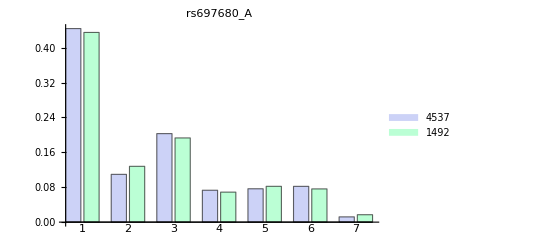

```mathematica
applyhist[subd[5,#][[;;,sym]]&/@{0,1},mystyle[data[[1,5]]]]
```

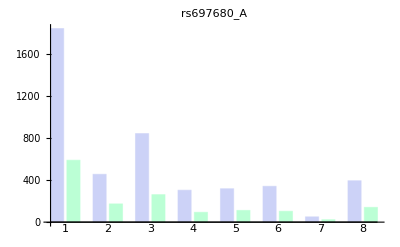
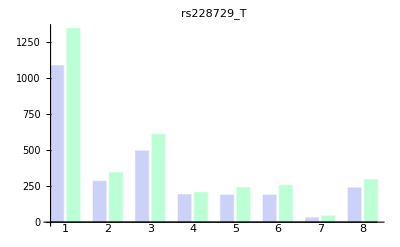

```mathematica
Table[applyhist[subd[var,#][[;;,sym]]&/@{0,1},mystyle[data[[1,var]]]],{var,5,6}]
```

```mathematica
tab=Table[Histogram[subd[var,#][[;;,sym]]&/@{0,1},Auto,"Probability",ChartLayout->"Stacked",PlotLabel->mystyle[data[[1,var]]]],{var,5,98}];
```

```mathematica
expdf0["test_sym_singlegene",Grid[ArrayReshape[tab,{10,10},""]]]
```

test_sym_singlegene.pdf